# Signal-1

```mathematica
Needs["FourierSeries`"]
```

```mathematica
Clear["Global`*"]
```

```mathematica
f={100,200,300,400};
```

```mathematica
ω=2 π f
```

{200 π,400 π,600 π,800 π}

```mathematica
signal=∑_(i=1)^Length[f] Sin[ω[[i]] t]
```

Sin[200 π t]+Sin[400 π t]+Sin[600 π t]+Sin[800 π t]

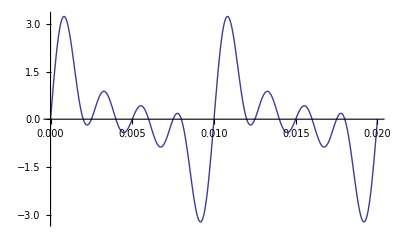

```mathematica
Plot[signal,{t,0,2/f[[1]]}]
```

```mathematica
play=Play[signal,{t,0,3}]
```

-Graphics-

## Export

### Get current notebook directory

```mathematica
CurrentNotebookDirectory=NotebookDirectory[SelectedNotebook[]]
```

/Users/Soha/Google Drive/Café Planck/1-Mathematics/Fourier analysis/07-FFT/

### Set Directory to current notebook directory

```mathematica
SetDirectory[CurrentNotebookDirectory]
```

/Users/Soha/Google Drive/Café Planck/1-Mathematics/Fourier analysis/07-FFT

### Get current notebook name without extension

```mathematica
CurrentNotebookName=StringTake[ToString[SelectedNotebook[]],{18,StringPosition[ToString[SelectedNotebook[]],">",1][[1,1]]-4}]
```

Signal-1

### Creat file name with extension

```mathematica
fileName=StringJoin[CurrentNotebookName,".wav"]
```

Signal-1.wav

### Export

```mathematica
Export[fileName,play]
```

Signal-1.wav